# Chimera: Chiral Measures Research Assistant

© Emilio Pisanty 2026

## Introduction

### Readme

The Mathematica package Chimera – Chiral Measures Research Assistant – contains code and tools useful to quantify the chirality of a distribution, and to apply those tools to photoelectron momentum spectra, such as might be obtained from strong-field ionization of chiral molecules, or of achiral systems driven by chiral fields.

(Expand the cell below for a brief package description which will be included in the package .m file)
TO DO: update this

```mathematica
(* Chimera: Chiral Measures Research Assistant *)
(* © Emilio Pisanty, 2025 *)

(* For more information, see https://github.com/????/???? *)

(*TODO - update this*)
```

### TO DO

- Check all functions have usage statements.
- Pull in helixDataDistribution as well as three-gaussians distributions?
- In sphericalDecompositionPlot, if the w3jproduct’s are all zero (cf. example in the notebook from 2024-11-27), throw an error and don’t attempt to plot.

- Build tensor visualization tools, both on the sphere and as surface 3D plots of the corresponding potential

-  Consider  removing Normal and returning a SymmetrizedArray object.

### Licensing

This package is licensed under ?????.

## Implementation

## Initialization

### Initialization and most package infrastructure

#### Package initialization

```mathematica
BeginPackage["Chimera`"];
```

#### Version number

The variable $ChimeraVersion gives the version of the Chimera package currently loaded, and its timestamp

```mathematica
$ChimeraVersion::usage="$ChimeraVersion prints the current version of the Chimera package in use and its timestamp.";
$ChimeraTimestamp::usage="$ChimeraTimestamp prints the timestamp of the current version of the Chimera package.";
Begin["`Private`"];
$ChimeraVersion:="Chimera v0.3, "<>$ChimeraTimestamp;
End[];
```

The timestamp is updated every time the notebook is saved via an appropriate notebook option, which is set by the code below.

```mathematica
SetOptions[
EvaluationNotebook[],
NotebookEventActions->{{"MenuCommand","Save"}:>(
NotebookWrite[
Cells[CellTags->"version-timestamp"]⟦1⟧,
Cell[
BoxData[RowBox[{"Begin[\"`Private`\"];$ChimeraTimestamp=\""<>DateString[]<>"\";End[];"}]]
,"Input",InitializationCell->True,CellTags->"version-timestamp"
],None,AutoScroll->False];
NotebookSave[]
),PassEventsDown->True}
];
```

To reset this behaviour to normal, evaluate the cell below

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions->{{"MenuCommand","Save"}:>(NotebookSave[]),PassEventsDown->True}]
```

#### Directory

```mathematica
$ChimeraDirectory::usage="$ChimeraDirectory is the directory where the current Chimera package instance is located.";
```

```mathematica
Begin["`Private`"];
With[{softLinkTestString=StringSplit[StringJoin[ReadList["! ls -la "<>StringReplace[$InputFileName,{" "->"\\ "}],String]]," -> "]},
If[Length[softLinkTestString]>1,(*Testing in case $InputFileName is a soft link to the actual directory.*)
$ChimeraDirectory=StringReplace[DirectoryName[softLinkTestString⟦2⟧],{" "->"\\ "}],
$ChimeraDirectory=StringReplace[DirectoryName[$InputFileName],{" "->"\\ "}];
]];
End[];
```

#### Git commit hash and message

```mathematica
$ChimeraCommit::usage="$ChimeraCommit returns the git commit log at the location of the Chimera package if there is one.";
$ChimeraCommit::OS="$ChimeraCommit has only been tested on Linux.";
```

```mathematica
Begin["`Private`"];
$ChimeraCommit:=(If[$OperatingSystem≠"Unix",Message[$ChimeraCommit::OS]];
StringJoin[Riffle[ReadList["!cd "<>$ChimeraDirectory<>" && git log -1",String],{"\n"}]]);
End[];
```

### Timestamp

#### Timestamp

```mathematica
Begin["`Private`"];$ChimeraTimestamp="Thu 29 Jan 2026 11:50:49";End[];
```

### Usage of the package-infrastructure variables

```mathematica
$ChimeraVersion
```

Chimera v1.0.0, Mon 13 Feb 2023 17:44:42

```mathematica
$ChimeraTimestamp
```

Mon 13 Feb 2023 17:44:42

```mathematica
$ChimeraDirectory
```

The $ChimeraCommit command only works if you have a working git repository on the same directory as the notebook file. It also (so far) only works on Linux.

```mathematica
$ChimeraCommit
```

## Package code

### General utilities

#### LRA

```mathematica
LR={"L","R"};
LRA={"L","R","A"};
```

#### XYZ

```mathematica
XYZ={"x","y","z"};
```

#### Sign on L, R, A

```mathematica
Unprotect[Sign];
Sign["L"]=1;
Sign["R"]=-1;
Sign["A"]=0;
Protect[Sign];
```

#### MegabyteCount

```mathematica
MegabyteCount[expr_]:=UnitConvert[Quantity[N@ByteCount[expr],"Bytes"],"Megabytes"]
```

#### electronCount

```mathematica
electronCount[data_,h_]:=electronCount[data,h]=Total[data[h][[All,4]]]
```

### Standardized data format

The standard format for data is as follows:

```mathematica
{px,py,pz,weight}
{px,py,pz,weight,p}
```

The weight can be an integer (e.g. number of counts) or a float (e.g. |ψ(p)|^2, or a direct value from an analytical probability density function). 

The fifth entry is optional, but recommended -- the total momentum p=√(px^2+py^2+pz^2). Ideally datasets should have this pre-computed right after import, and this entry can then be used for binning: to create histograms over momentum, to bin together for calculating spherical decompositions, etc.

As a general rule, the import process should remove any records for which weight=0.

### General functions

#### SolidHarmonicS

This function implements the solid harmonic S_(l,m)(r)=√((4π)/(2l+1))r^l Y_(l,m)(θ,ϕ), which is a homogeneous polynomial of degree l, and lends itself much better to symbolic differentiation than explicit spherical harmonics.

The code below implements the identity

    S_(l m)(x,y,z)=√((l+m)!(l-m)!)∑_(p,q,r) 1/(p!q!r!)(-(x+i y)/2)^p((x-i y)/2)^q z^r
    
Provided as Eq. (16), §5.1.7, in D. A. Varshalovich, A. N. Moskalev, and V. K. Khersonskii, Quantum Theory Of Angular Momentum (Singapore, 1988), handle:20.500.12657/50493. The code implementation uses multiple ideas used by Jan Mangaldan (J.M.) in his answer at http://mathematica.stackexchange.com/a/124336/1000, subsequently published in the Wolfram Function Repository as ResourceFunction["SolidHarmonicR"]. This package includes the explicit definition below in the spirit of backwards compatibility, and because the formula from Varshalovich et al. provides better formulas for MultipolarBasisTensorT.

```mathematica
SolidHarmonicS::usage="SolidHarmonicS[l,m,x,y,z] calculates the solid harmonic S_lm(x,y,z)=r^lY_lm(x,y,z).

SolidHarmonicS[l,m,{x,y,z}] does the same.";
Begin["`Private`"];

dpower[x_,y_]:=Piecewise[{{1,y==0}},x^y]

SolidHarmonicS[λ_Integer,μ_Integer,x_,y_,z_]/;λ≥Abs[μ]:=Times[
(*Sqrt[(2 λ+1)/(4 π)],*)
Sqrt[(λ-μ)!(λ+μ)!],
Sum[If[
Or[p+q+r!=λ,p-q!=μ],0,
Times[
1/(p!q!r!),
dpower[-(x+ⅈ y)/2,p],
dpower[(x-ⅈ y)/2,q],
dpower[z,r]
]],{p,0,λ},{q,0,λ},{r,0,λ}]
]
SolidHarmonicS[λ_Integer,μ_Integer,{x_,y_,z_}]/;λ≥Abs[μ]:=SolidHarmonicS[λ,μ,x,y,z]
End[];
```

Benchmarking:

```mathematica
Table[
Table[
(*{l,m}->*)(*Simplify@*)SolidHarmonicS[l,m,{x,y,z}]
,{m,-l,l}]
,{l,0,5}]//TableForm
```

1 |  |  |  |  |  |  |  |  |  | 
(x-ⅈ y)/(√2) | z | (-x-ⅈ y)/(√2) |  |  |  |  |  |  |  | 
1/2 √(3/2) (x-ⅈ y)^2 | √(3/2) (x-ⅈ y) z | 2 (1/4 (-x-ⅈ y) (x-ⅈ y)+z^2/2) | √(3/2) (-x-ⅈ y) z | 1/2 √(3/2) (-x-ⅈ y)^2 |  |  |  |  |  | 
1/4 √5 (x-ⅈ y)^3 | 1/2 √(15/2) (x-ⅈ y)^2 z | 4 √3 (1/16 (-x-ⅈ y) (x-ⅈ y)^2+1/4 (x-ⅈ y) z^2) | 6 (1/4 (-x-ⅈ y) (x-ⅈ y) z+z^3/6) | 4 √3 (1/16 (-x-ⅈ y)^2 (x-ⅈ y)+1/4 (-x-ⅈ y) z^2) | 1/2 √(15/2) (-x-ⅈ y)^2 z | 1/4 √5 (-x-ⅈ y)^3 |  |  |  | 
1/8 √(35/2) (x-ⅈ y)^4 | 1/4 √35 (x-ⅈ y)^3 z | 12 √10 (1/96 (-x-ⅈ y) (x-ⅈ y)^3+1/16 (x-ⅈ y)^2 z^2) | 12 √5 (1/16 (-x-ⅈ y) (x-ⅈ y)^2 z+1/12 (x-ⅈ y) z^3) | 24 (1/64 (-x-ⅈ y)^2 (x-ⅈ y)^2+1/8 (-x-ⅈ y) (x-ⅈ y) z^2+z^4/24) | 12 √5 (1/16 (-x-ⅈ y)^2 (x-ⅈ y) z+1/12 (-x-ⅈ y) z^3) | 12 √10 (1/96 (-x-ⅈ y)^3 (x-ⅈ y)+1/16 (-x-ⅈ y)^2 z^2) | 1/4 √35 (-x-ⅈ y)^3 z | 1/8 √(35/2) (-x-ⅈ y)^4 |  | 
3/16 √7 (x-ⅈ y)^5 | 3/8 √(35/2) (x-ⅈ y)^4 z | 48 √35 (1/768 (-x-ⅈ y) (x-ⅈ y)^4+1/96 (x-ⅈ y)^3 z^2) | 12 √210 (1/96 (-x-ⅈ y) (x-ⅈ y)^3 z+1/48 (x-ⅈ y)^2 z^3) | 24 √30 (1/384 (-x-ⅈ y)^2 (x-ⅈ y)^3+1/32 (-x-ⅈ y) (x-ⅈ y)^2 z^2+1/48 (x-ⅈ y) z^4) | 120 (1/64 (-x-ⅈ y)^2 (x-ⅈ y)^2 z+1/24 (-x-ⅈ y) (x-ⅈ y) z^3+z^5/120) | 24 √30 (1/384 (-x-ⅈ y)^3 (x-ⅈ y)^2+1/32 (-x-ⅈ y)^2 (x-ⅈ y) z^2+1/48 (-x-ⅈ y) z^4) | 12 √210 (1/96 (-x-ⅈ y)^3 (x-ⅈ y) z+1/48 (-x-ⅈ y)^2 z^3) | 48 √35 (1/768 (-x-ⅈ y)^4 (x-ⅈ y)+1/96 (-x-ⅈ y)^3 z^2) | 3/8 √(35/2) (-x-ⅈ y)^4 z | 3/16 √7 (-x-ⅈ y)^5

```mathematica
Table[
Table[
(*{l,m}->*)Simplify[√((2l+1)/(4π))SolidHarmonicS[l,m,r{Sin[θ]Cos[φ],Sin[θ]Sin[φ],Cos[θ]}]/(r^l SphericalHarmonicY[l,m,θ,φ])]
,{m,-l,l}]
,{l,0,5}]
```

{{1},{1,1,1},{1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1}}

How many terms actually contribute to the sum?

```mathematica
Table[
Table[
Tooltip[Length[#],{l,m}->#/.{contr->List}]&@Flatten[Table[
If[
Or[p+q+r!=l,p-q!=m],Nothing,contr[p,q,r]
]
,{p,0,l},{q,0,l},{r,0,l}]]
,{m,-l,l}]
,{l,0,6}]//TableForm
```

1 |  |  |  |  |  |  |  |  |  |  |  | 
1 | 1 | 1 |  |  |  |  |  |  |  |  |  | 
1 | 1 | 2 | 1 | 1 |  |  |  |  |  |  |  | 
1 | 1 | 2 | 2 | 2 | 1 | 1 |  |  |  |  |  | 
1 | 1 | 2 | 2 | 3 | 2 | 2 | 1 | 1 |  |  |  | 
1 | 1 | 2 | 2 | 3 | 3 | 3 | 2 | 2 | 1 | 1 |  | 
1 | 1 | 2 | 2 | 3 | 3 | 4 | 3 | 3 | 2 | 2 | 1 | 1

#### cleanContourPlot

This function cleans up automatically generated contour plots. Generically, a contour plot is made of a Polygon with a vast number of vertices in its interior, which are not necessary and only slow the plot down - including a large use of CPU when the mouse hovers above it, which is definitely unwanted. (In addition, these polygons can give rise to white edges inside each contour when printed to pdf, which is also undesirable.) This function changes such Polygons to FilledCurve constructs which no longer contain the unwanted mid-contour points.

This function was written by Szabolcs Horvát (http://mathematica.stackexchange.com/users/12/szabolcs) and was originally posted at http://mathematica.stackexchange.com/a/3279 under a CC-BY-SA license.

```mathematica
cleanContourPlot::usage="cleanContourPlot[plot] Cleans up a contour plot by coalescing complex polygons into single FilledCurve instances. See MM.SE/a/3279 for source and documentation.";
```

```mathematica
Begin["`Private`"];
cleanContourPlot[cp_] :=
 Module[{points, groups, regions, lines},
  groups = 
   Cases[cp, {style__, g_GraphicsGroup} :> {{style}, g}, Infinity];
  points = 
   First@Cases[cp, GraphicsComplex[pts_, ___] :> pts, Infinity];
  regions = Table[
    Module[{group, style, polys, edges, cover, graph},
     {style, group} = g;
     polys = Join @@ Cases[group, Polygon[pt_, ___] :> pt, Infinity];
     edges = Join @@ (Partition[#, 2, 1, 1] & /@ polys);
     cover = Cases[Tally[Sort /@ edges], {e_, 1} :> e];
     graph = Graph[UndirectedEdge @@@ cover];
     {Sequence @@ style, 
      FilledCurve[
       List /@ Line /@ First /@ 
          Map[First, 
           FindEulerianCycle /@ (Subgraph[graph, #] &) /@ 
             ConnectedComponents[graph], {3}]]}
     ],
    {g, groups}];
  lines = Cases[cp, _Tooltip, Infinity];
  Graphics[GraphicsComplex[points, {regions, lines}], 
   Sequence @@ Options[cp]]
  ]
End[];
```

### Photoelectron spectra

#### photoElectronSpectrum

```mathematica
photoElectronSpectrum::usage="photoElectronSpectrum[data,Δp] returns a histogram photoelectron spectrum for the given data set, which must be in the standard format, using bin width Δp.";

Begin["`Private`"];

photoElectronSpectrum[dataSet_,pBin_,options___]:=Block[{dataSet2,histogramAssoc},
If[
Dimensions[dataSet][[2]]==5,
dataSet2=dataSet,
dataSet2=Map[Join[#,{Norm[#[[1;;3]]]}]&,dataSet]
];
histogramAssoc=Map[
Total,
KeySort[GroupBy[dataSet2,Floor[#[[5]],pBin]&]][[1;;,All,4]]
];
Show[{
Graphics[{
EdgeForm[{Opacity[0.665],Thickness[Small]}],
FaceForm[RGBColor[0.987148, 0.8073604000000001, 0.49470040000000004]],
KeyValueMap[
Function[{p,value},Rectangle[{p,0},{p+pBin,value}]],
histogramAssoc
]
}]
}
,options
,Frame->True
,ImageSize->400
,AspectRatio->1/1.6
,PlotRangePadding->{{None,None},{None,Scaled[0.07]}}
]
]

End[];
```

#### photoElectronSpectrumList

```mathematica
photoElectronSpectrumList::usage="photoElectronSpectrumList[data,range,Δp] returns a histogram photoelectron spectrum for the data sets data[h], where h covers the given range, using bin width Δp.";

Begin["`Private`"];

photoElectronSpectrumList[dataSet_,range_,pBin_,options___]:=Map[
photoElectronSpectrum[dataSet[#],pBin,options,PlotLabel->#]&,
range]

End[];
```

### Spherical decomposition

#### Testing symmetry of spherical harmonics

From the SphericalHarmonicY docs: “For l≥0, Y_l^m(θ,ϕ)=√((2l+1)/(4π))√((l-m)!/(l+m)!)P_l^m(cos(θ))e^imϕ where P_l^m is the associated Legendre function. “

First off: a sanity check to make sure that SphericalHarmonicY and SolidHarmonicS do indeed match.

```mathematica
Table[Table[
Simplify[
SphericalHarmonicY[ℓ,m,θ,ϕ]==SolidHarmonicS[ℓ,m,FromSphericalCoordinates[{1,θ,ϕ}]]
]
,{m,-ℓ,ℓ}],{ℓ,0,4}]
```

{{True},{True,True,True},{True,True,True,True,True},{True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True}}

The symmetry of the spherical harmonics: changing the sign of m is equivalent to conjugation with a global sign of (-1)^m.

```mathematica
Table[Table[
Simplify[
(-1)^m SphericalHarmonicY[ℓ,m,θ,ϕ]*==SphericalHarmonicY[ℓ,-m,θ,ϕ]
,Assumptions->{{θ,ϕ}>0}
]
,{m,0,ℓ}],{ℓ,0,5}]
```

{{True},{True,True},{True,True,True},{True,True,True,True},{True,True,True,True,True},{True,True,True,True,True,True}}

The (-1)^m sign comes from the Legendre factor P_ℓ^m(cos(θ)):

```mathematica
Table[Table[
Sign[Simplify[
LegendreP[ℓ,m,Cos[θ]]/LegendreP[ℓ,-m,Cos[θ]]
]]
,{m,0,ℓ}],{ℓ,0,5}]
```

{{1},{1,-1},{1,-1,1},{1,-1,1,-1},{1,-1,1,-1,1},{1,-1,1,-1,1,-1}}

#### SetSphericalDecomposition

```mathematica
SetSphericalDecomposition::usage="SetSphericalDecomposition[ρSymbol,dataSet] creates memoizable definitions for ρSymbol[h,ℓ,m,{pmin,pmax}] to be the spherical decomposition with angular-momentum numbers ℓ,m over momentum bin {pmin,pmax} for the dataset dataSet[h].";

Begin["`Private`"];

SetSphericalDecomposition[ρSymbol_,dataSet_]:=Block[{},
ρSymbol::usage=StringJoin[
ToString[ρSymbol],
"[h,ℓ,m,{pmin,pmax}] memoizes and returns the spherical decomposition with angular-momentum numbers ℓ,m over momentum bin {pmin,pmax} for the dataset ",
ToString[dataSet],
"[h]."
];
SetSharedFunction[ρSymbol];

ρSymbol[h_,ℓ_,m_/;(m>=0),{pmin_,pmax_}]:=Parallel`Developer`SendBack[
ρSymbol[h,ℓ,m,{pmin,pmax}]=Block[{momentumFilteredData},
momentumFilteredData=Select[dataSet[h],pmin<#[[5]]<pmax&];
1/electronCount[dataSet,h] Sum[
record[[4]]SolidHarmonicS[ℓ,m,record[[1;;3]]]*
,{record,momentumFilteredData}]
]
];
ρSymbol[h_,ℓ_,m_/;(m<0),{pmin_,pmax_}]:=(-1)^m Conjugate[ρSymbol[h,ℓ,-m,{pmin,pmax}]]
]

End[];
```

The Parallel`Developer`SendBack[] call is to ensure proper parallelization of the memoized definitions, as per https://mathematica.stackexchange.com/a/125307/1000

#### SetExactSphericalDecomposition

```mathematica
Options[SetExactSphericalDecomposition]=Options[NIntegrate];

SetExactSphericalDecomposition::usage="SetExactSphericalDecomposition[ρSymbol,PDF] creates memoizable definitions for ρSymbol[h,ℓ,m,{pmin,pmax}] to be the spherical decomposition with angular-momentum numbers ℓ,m over momentum bin {pmin,pmax} for the symbolic probability density function PDF[h].";

Begin["`Private`"];

SetExactSphericalDecomposition[ρSymbol_,PDF_,options:OptionsPattern[]]:=Block[{},
ρSymbol::usage=StringJoin[
ToString[ρSymbol],
"[h,ℓ,m,{pmin,pmax}] memoizes and returns the spherical decomposition with angular-momentum numbers ℓ,m over momentum bin {pmin,pmax}, numerically integrated for the PDF ",
ToString[PDF],
"[h]."
];
ρSymbol::integrationError="Encountered integration errors in the calculation of "<>ToString[ρSymbol]<>" with parameters {h,ℓ,m,{pmin,pmax}}= `1`.";
ρSymbol::integrating="Beginning numerical integration for "<>ToString[ρSymbol]<>"[`1`,`2`,`3`,`4`]";
Off[ρSymbol::integrating];
SetSharedFunction[ρSymbol];

ρSymbol[h_,ℓ_,m_/;(m>=0),{pmin_,pmax_}]:=Parallel`Developer`SendBack[
ρSymbol[h,ℓ,m,{pmin,pmax}]=Block[{pdf,fromSphericalCoordinates,integral},
pdf[{p_,θ_,ϕ_}]:=PDF[h][p,θ,ϕ];
fromSphericalCoordinates[{pp_,θ_,ϕ_}]=FromSphericalCoordinates[{pp,θ,ϕ}];
Message[ρSymbol::integrating,h,ℓ,m,{pmin,pmax}];

Check[
integral=NIntegrate[
Times[
pdf[fromSphericalCoordinates[{p,θ,ϕ}]],
SolidHarmonicS[ℓ,m,fromSphericalCoordinates[{p,θ,ϕ}]]*,
p^2 Sin[θ]
],{θ,0,π},{ϕ,0,2π},{p,pmin,pmax}
,Evaluate[Sequence@@FilterRules[{options},Options[NIntegrate]]]
],
Message[ρSymbol::integrationError,{h,ℓ,m,{pmin,pmax}}];
integral
]
]
];
ρSymbol[h_,ℓ_,m_/;(m<0),{pmin_,pmax_}]:=(-1)^m Conjugate[ρSymbol[h,ℓ,-m,{pmin,pmax}]]
]

End[];
```

Note the use of an explicit symbolic version of fromSphericalCoordinates. This is to avoid errors thrown up by the standard FromSphericalCoordinates[{p,θ,ϕ}] when ϕ∈(π,2π) and when ϕ=-π.

#### SetSymbolicSphericalDecomposition

As pointed out in JM (in https://mathematica.stackexchange.com/a/6846/1000), the built-in route is to use Expectation[].

```mathematica
Options[SetSymbolicSphericalDecomposition]={Assumptions->{}}(*Options[NIntegrate]*);

SetSymbolicSphericalDecomposition::usage="SetSymbolicSphericalDecomposition[ρSymbol,distribution] creates memoizable definitions for ρSymbol[ℓ,m] to be the spherical decomposition with angular-momentum numbers ℓ,m over momentum space for the given symbolic distribution.";

Begin["`Private`"];

SetSymbolicSphericalDecomposition[ρSymbol_,distribution_,options:OptionsPattern[]]:=Block[{},
ρSymbol::usage=StringJoin[
ToString[ρSymbol],
"[ℓ,m] memoizes and returns the spherical decomposition with angular-momentum numbers ℓ,m, symbollically calculated for the distribution ",
ToString[distribution],
"."
];
(*ρSymbol::integrationError="Encountered integration errors in the calculation of "<>ToString[ρSymbol]<>" with parameters {h,ℓ,m}= `1`.";*)
ρSymbol::integrating="Beginning symbolic integration for "<>ToString[ρSymbol]<>"[`1`,`2`]";
Off[ρSymbol::integrating];
SetSharedFunction[ρSymbol];

ρSymbol[ℓ_,m_/;(m>=0)]:=Parallel`Developer`SendBack[
ρSymbol[ℓ,m]=Block[{px,py,pz},
Message[ρSymbol::integrating,ℓ,m];
Expectation[
SolidHarmonicS[ℓ,m,{px,py,pz}]/.{ⅈ->-ⅈ},
{px,py,pz}\[Distributed]distribution
]
]
];
ρSymbol[ℓ_,m_/;(m<0)]:=Simplify[
(-1)^m Conjugate[ρSymbol[ℓ,-m]]
,Assumptions->OptionValue[Assumptions]
]
]

End[];
```

```mathematica
ClearAll[ρSyntheticSymbolicL];
SetSymbolicSphericalDecomposition[ρSyntheticSymbolicL,syntheticDataDistribution["L"]]
```

```mathematica
Table[m->AbsoluteTiming[ρSyntheticSymbolicL[2,m]],{m,-2,2}]
```

{-2→{0.0722775,0.0206013},-1→{0.0494435,0},0→{0.0499457,0.275442},1→{0.0473495,0},2→{0.0491292,0.0206013}}

```mathematica
ClearAll[ρHelixSymbolic2];
SetSymbolicSphericalDecomposition[ρHelixSymbolic2,helixDataDistribution[2,{px0,σ1,σ2,α}],Assumptions->helixDataAssumptions]
```

```mathematica
Table[m->AbsoluteTiming[ρHelixSymbolic2[2,m]],{m,-2,2}]
```

{-2→{0.061174,1/8 √(15/(2 π)) (2 px0^2+σ1^2-σ2^2+(-σ1^2+σ2^2) Cos[2 α])},-1→{0.0389874,0},0→{0.0446311,-1/8 √(5/π) (2 px0^2+σ1^2-σ2^2+3 σ1^2 Cos[2 α]-3 σ2^2 Cos[2 α])},1→{1.8×10^-6,0},2→{1.7×10^-6,1/8 √(15/(2 π)) (2 px0^2+σ1^2-σ2^2-σ1^2 Cos[2 α]+σ2^2 Cos[2 α])}}

```mathematica
helixDataAssumptions
```

{(px0|α)∈ℝ,{σ1,σ2}>0}

#### ρ1mToCartesian

Getting the cartesian components out of the solid harmonics:

```mathematica
Simplify[√((2π)/3)(SolidHarmonicS[1,1,{x,y,z}]-SolidHarmonicS[1,-1,{x,y,z}])/-1]
Simplify[√((2π)/3)(SolidHarmonicS[1,1,{x,y,z}]+SolidHarmonicS[1,-1,{x,y,z}])/-ⅈ]
√((4π)/3)SolidHarmonicS[1,0,{x,y,z}]
```

x

y

z

.... buuuuut, the definition of ρ_(ℓ m) involves Y_(ℓ m)(θ,ϕ)*, i.e. against the conjugate, so we need to include that.

```mathematica
Simplify[√((2π)/3)(SolidHarmonicS[1,1,{x,y,z}]*-SolidHarmonicS[1,-1,{x,y,z}]*)/-1,Assumptions->{{x,y,z}∈Reals}]
Simplify[√((2π)/3)(SolidHarmonicS[1,1,{x,y,z}]*+SolidHarmonicS[1,-1,{x,y,z}]*)/ⅈ,Assumptions->{{x,y,z}∈Reals}]
Simplify[√2 √((2π)/3)SolidHarmonicS[1,0,{x,y,z}]*,Assumptions->{{x,y,z}∈Reals}]
```

x

y

z

```mathematica
ρ1mToCartesian::usage="ρ1mToCartesian[{ρ1m1,ρ10,ρ11}]";

Begin["`Private`"];

ρ1mToCartesian[{ρ1m1_,ρ10_,ρ11_}]:=Chop[√((2π)/3){(ρ11-ρ1m1)/-1,(ρ11+ρ1m1)/ⅈ,√2 ρ10}]

End[];
```

#### ρToCenterOfMass

```mathematica
2 √π SolidHarmonicS[0,0,{x,y,z}]
```

1

```mathematica
ρToCenterOfMass::usage="ρToCenterOfMass[{{ρ00},{ρ1m1,ρ10,ρ11}}]";

Begin["`Private`"];

ρToCenterOfMass[{{ρ00_},{ρ1m1_,ρ10_,ρ11_}}]:=Chop[(√((2π)/3){(ρ11-ρ1m1)/-1,(ρ11+ρ1m1)/ⅈ,√2 ρ10})/(2 √π ρ00)]

End[];
```

This form for the input is to allow a natural calculation for the ρ inside:

```mathematica
ρToCenterOfMass[
Table[Table[
ρ[ℓ,m,p]
,{m,-ℓ,ℓ}],{ℓ,0,1}]
]
```

#### COM exact

```mathematica
FromSphericalCoordinates[{p,θ,ϕ}]
```

{p Cos[ϕ] Sin[θ],p Sin[θ] Sin[ϕ],p Cos[θ]}

```mathematica
ClearAll[COMfromPDF];

COMfromPDF::usage="COMfromPDF[PDF,{pmin,pmax},]";

Options[COMfromPDF]=Join[{PrecisionGoal->8,AccuracyGoal->8},DeleteCases[Options[NIntegrate],Alternatives[PrecisionGoal->_,AccuracyGoal->_]]];

COMfromPDF::integrationError="Encountered integration errors in the calculation of COMfromPDF with pdf `1` and {pmin,pmax}= `2`.";

SetSharedFunction[COMfromPDF];

Begin["`Private`"];

COMfromPDF[PDF_,{pmin_,pmax_},options:OptionsPattern[]]:=COMfromPDF[PDF,{pmin,pmax},options]=Block[{pdf,fromSphericalCoordinates,integrals},
pdf[{p_,θ_,ϕ_}]:=PDF[p,θ,ϕ];
fromSphericalCoordinates[{pp_,θ_,ϕ_}]=FromSphericalCoordinates[{pp,θ,ϕ}];

Check[
integrals=NIntegrate[
Times[
pdf[fromSphericalCoordinates[{p,θ,ϕ}]],
Join[{1},fromSphericalCoordinates[{p,θ,ϕ}]],
p^2 Sin[θ]
],{θ,0,π},{ϕ,-π,π},{p,pmin,pmax}
,Evaluate[Sequence@@FilterRules[{options},Options[NIntegrate]]]
];,
Message[COMfromPDF::integrationError,PDF,{pmin,pmax}];
];

;

integrals[[2;;4]]/integrals[[1]]
]

End[];
```

```mathematica
COMfromPDF[syntheticDataPDF["L"],{0.4,0.5}]
```

{0.165329,0.084463,0.038889}

Note the use of an explicit symbolic version of fromSphericalCoordinates. This is to avoid errors thrown up by the standard FromSphericalCoordinates[{p,θ,ϕ}] when ϕ∈(π,2π) and when ϕ=-π.

#### COM exact, cartesian

```mathematica
ClearAll[COMfromPDFcartesian];

COMfromPDFcartesian::usage="COMfromPDFcartesian[PDF,{pmin,pmax}]";

Options[COMfromPDFcartesian]=Join[{PrecisionGoal->8,AccuracyGoal->8},DeleteCases[Options[NIntegrate],Alternatives[PrecisionGoal->_,AccuracyGoal->_]]];

COMfromPDFcartesian::integrationError="Encountered integration errors in the calculation of COMfromPDFcartesian with pdf `1` and {pmin,pmax}= `2`.";

COMfromPDFcartesian::integrating="Beginning numerical integration for COMfromPDFcartesian[`1`,`2`]";
(*Off[COMfromPDFcartesian::integrating];*)

SetSharedFunction[COMfromPDFcartesian];

Begin["`Private`"];

COMfromPDFcartesian[PDF_,{pmin_,pmax_},options:OptionsPattern[]]:=COMfromPDFcartesian[PDF,{pmin,pmax},options]=Block[{integrals},
Message[COMfromPDFcartesian::integrating,PDF,{pmin,pmax}];

Check[
integrals=NIntegrate[
Times[
PDF[px,py,pz],
{1,px,py,pz},
Boole[pmin^2<px^2+py^2+pz^2<pmax^2]
],{px,-pmax,pmax},{py,-pmax,pmax},{pz,-pmax,pmax}
,Evaluate[Sequence@@FilterRules[{options},Options[NIntegrate]]]
];,
Message[COMfromPDFcartesian::integrationError,PDF,{pmin,pmax}];
];

;

integrals[[2;;4]]/integrals[[1]]
]

End[];
```

```mathematica
Off[COMfromPDFcartesian::integrating]
```

```mathematica
On[COMfromPDFcartesian::integrating]
```

```mathematica
COMfromPDFcartesian[exaggeratedDataPDF["L"],{0.6,0.7}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.54208×10^-8-2.32074×10^-34 ⅈ and 1.39892×10^-9 for the integral and error estimates.

COMfromPDFcartesian::integrationError: Encountered integration errors in the calculation of COMfromPDFcartesian with pdf exaggeratedDataPDF[L] and {pmin,pmax}= {0.6,0.7}.

{0.402821,0.00890088,4.04581×10^-6}

Global`COMfromPDFcartesian::shdw: Symbol COMfromPDFcartesian appears in multiple contexts {Global`,Chimera`}; definitions in context Global` may shadow or be shadowed by other definitions.

.... this seems to be too slow to be worth using...

### Chirality measures

#### SetChiralityMeasure

```mathematica
ClearAll[SetChiralityMeasure]
```

```mathematica
SetChiralityMeasure::usage="SetChiralityMeasure[χSymbol,ρSymbol] creates memoizable definitions for χSymbol[h,{ℓ1,ℓ2,ℓ3},{p1,p2,p3},Δp], which return the spherical chirality measure formed from the spherical decomposition ρSymbol with  helicity h, angular-momentum combination {ℓ1,ℓ2,ℓ3}, and with the corresponding spherical decompositions integrated between momenta p1, p2, p3 and p1+Δp, p2+Δp, p3+Δp, respectively.";

Begin["`Private`"];

SetChiralityMeasure[measureSymbol_,ρSymbol_]:=Block[{},
measureSymbol::usage=StringJoin[
ToString[measureSymbol],
"[h,{ℓ1,ℓ2,ℓ3},{p1,p2,p3},Δp] memoizes and returns the spherical chirality measure formed from the spherical decomposition ",
ToString[ρSymbol]," with the angular-momentum combination {ℓ1,ℓ2,ℓ3}, and with the corresponding spherical decompositions integrated between momenta p1, p2, p3 and p1+Δp, p2+Δp, p3+Δp, respectively."
];


measureSymbol[h_,{ℓ1_,ℓ2_,ℓ3_},{p1_,p2_,p3_},Δp_]:=Block[{},

(*Print["Beginning calculation of chirality measure ",measureSymbol," at parameters ",{h,{ℓ1,ℓ2,ℓ3},{p1,p2,p3},Δp}];*)

Sum[
If[
m1+m2+m3==0,
Times[
Quiet[
ThreeJSymbol[{ℓ1,m1},{ℓ2,m2},{ℓ3,m3}]
,ClebschGordan::phy],
ρSymbol[h,ℓ1,m1,{p1,p1+Δp}],
ρSymbol[h,ℓ2,m2,{p2,p2+Δp}],
ρSymbol[h,ℓ3,m3,{p3,p3+Δp}]
],
0
]
,{m1,-ℓ1,ℓ1},{m2,-ℓ2,ℓ2},{m3,-ℓ3,ℓ3}
]
]
]
End[];
```

#### SetSymbolicChiralityMeasure

```mathematica
ClearAll[SetSymbolicChiralityMeasure]
```

```mathematica
SetSymbolicChiralityMeasure::usage="SetSymbolicChiralityMeasure[χSymbol,ρSymbol] creates memoizable definitions for χSymbol[{ℓ1,ℓ2,ℓ3}], which return the spherical chirality measure formed from the spherical decomposition ρSymbol with the angular-momentum combination {ℓ1,ℓ2,ℓ3}.";

Begin["`Private`"];

SetSymbolicChiralityMeasure[measureSymbol_,ρSymbol_]:=Block[{},
measureSymbol::usage=StringJoin[
ToString[measureSymbol],
"[{ℓ1,ℓ2,ℓ3}] memoizes and returns the spherical chirality measure formed from the spherical decomposition ",
ToString[ρSymbol]," with the angular-momentum combination {ℓ1,ℓ2,ℓ3}."
];


measureSymbol[{ℓ1_,ℓ2_,ℓ3_}]:=Block[{},

(*Print["Beginning calculation of chirality measure ",measureSymbol," at parameters ",{h,{ℓ1,ℓ2,ℓ3},{p1,p2,p3},Δp}];*)

Sum[
If[
m1+m2+m3==0,
Times[
Quiet[
ThreeJSymbol[{ℓ1,m1},{ℓ2,m2},{ℓ3,m3}]
,ClebschGordan::phy],
ρSymbol[ℓ1,m1],
ρSymbol[ℓ2,m2],
ρSymbol[ℓ3,m3]
],
0
]
,{m1,-ℓ1,ℓ1},{m2,-ℓ2,ℓ2},{m3,-ℓ3,ℓ3}
]
]
]

End[];
```

### Plotting functions

#### scaleBar

```mathematica
scaleBar::usage="scaleBar[χMax]";

Begin["`Private`"];
scaleBar[χMax_]:=ContourPlot[
y,{x,0,1},{y,-χMax,χMax}
,ImageSize->{{350},{350}}
,PlotRangePadding->None
,Contours->χMax×Subdivide[-1.,1,16]
,ColorFunctionScaling->False
,ColorFunction->Function[Directive[Blend[{{-1,Blue},{0,White},{1,Red}},#/χMax]]]
,AspectRatio->15
,FrameTicks->{{None,χMax×Subdivide[-1.,1,16][[1;;;;2]]},{None,None}}
]

End[];
```

#### plotCOMvectorDirect

```mathematica
Begin["`Private`"];
plotCOMvectorDirect[COMvector_,color_:Darker[Red]]:=Block[{COM=COMvector},
Graphics3D[{
color,
Tube[{{0,0,0},0.9COM},0.02Norm[COM]],
Cone[{0.85COM,COM},0.05Norm[COM]]
}]
]
End[];
```

This uses a combination of Tube[] and Cone[] instead of a simpler Arrow[Tube[]] construct in order to have a consistent size of the arrowhead (relative to the arrow itself) that is independent of the size of the graphic that the arrow is embedded into.

```mathematica
plotCOMvectorDirect[COMfromPDF[syntheticDataPDF["L"],{0.4,0.5}]]
```

-Graphics3D-

#### plotCOMvector

```mathematica
Begin["`Private`"];

plotCOMvector[ρSymbol_,h_,pInt_]:=Block[{COM},
COM=ρToCenterOfMass[
Table[Table[
ρSymbol[h,ℓ,m,pInt]
,{m,-ℓ,ℓ}],{ℓ,0,1}]
];

plotCOMvectorDirect[COM]
(*Graphics3D[{
Darker[Red],
Tube[{{0,0,0},0.9COM},0.02Norm[COM]],
Cone[{0.85COM,COM},0.075Norm[COM]]
}]*)
]

End[];
```

#### plotDistributionOnSphere

Plotting a function (multipolar or otherwise) over a sphere as explained in the following Stack Exchange threads	:

https://physics.stackexchange.com/a/65660/8563
https://physics.stackexchange.com/q/336512/8563

```mathematica
Begin["`Private`"];

plotDistributionOnSphere[distribution_,p_,options:OptionsPattern[]]:=Block[{max},
max=NMaximize[
distribution@@FromSphericalCoordinates[{p,θ,ϕ}]Sin[θ]
,{θ,ϕ}][[1]];
ContourPlot3D[
px^2+py^2+pz^2==p^2
,{px,-1.1p,1.1p},{py,-1.1p,1.1p},{pz,-1.1p,1.1p}
,options
,ColorFunctionScaling->False
,ColorFunction->Function[{px,py,pz,pp},Blend[{RGBColor[1,1,1,0],Darker[Red,0.3]},1/max distribution[px,py,pz]]]
,MeshFunctions->{#1&,#2&,#3&,distribution[#1,#2,#3]&}
,MeshStyle->{Directive[GrayLevel[0.3],Opacity[0.25]],Directive[GrayLevel[0.3],Opacity[0.25]],Directive[GrayLevel[0.3],Opacity[0.25]],Black}
,Mesh->{10,10,10,15}
,AxesLabel->{"p_x","p_y","p_z"}
,SphericalRegion->True
,ImageSize->500
,PerformanceGoal->"Quality"
]
]

End[];
```

```mathematica
plotDistributionOnSphere[syntheticDataPDF["L"],1.4,PlotPoints->90,MaxRecursion->5]
```

(output removed)

```mathematica
plotDistributionOnSphere[syntheticDataPDF["L"],0.9,PlotPoints->50]
```

(output removed)

#### contourPlotOfDistributionOverSphericalShell

```mathematica
Begin["`Private`"];

contourPlotOfDistributionOverSphericalShell[distribution_,p_,options:OptionsPattern[]]:=Block[{max},
max=NMaximize[
distribution@@FromSphericalCoordinates[{p,θ,ϕ}]Sin[θ]
,{θ,ϕ}][[1]];
cleanContourPlot[
ContourPlot[
Evaluate[
distribution@@FromSphericalCoordinates[{p,θ,ϕ}]Sin[θ]
]
,{ϕ,0,2π},{θ,0,π}
,options
,PlotRangePadding->None
,AspectRatio->Automatic
,ImageSize->500
,PlotRange->Full
,ColorFunctionScaling->False
,ColorFunction->Function[dist,Blend[{RGBColor[1,1,1,0],Darker[Red,0.3]},1/max dist]]
]
]
]

End[];
```

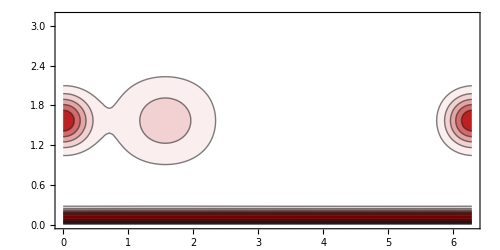

```mathematica
contourPlotOfDistributionOverSphericalShell[syntheticDataPDF["L"],1.0,PlotPoints->50]
```

#### plotCOMvectorTrio

```mathematica
Begin["`Private`"];

plotCOMvectorTrio[ρSymbol_,h_,pIntervals_]:=Block[{COMs,s},
COMs=Table[
ρToCenterOfMass[
Table[Table[
ρSymbol[h,ℓ,m,pInt]
,{m,-ℓ,ℓ}],{ℓ,0,1}]
]
,{pInt,pIntervals}];
s=Mean[Norm/@COMs];

Show[{
Graphics3D[{
Darker[Red],
Table[{
Tube[{{0,0,0},0.9COM},0.02s],
Cone[{(1-0.15s)COM,COM},0.075s]
},{COM,COMs}],
Opacity[0.1],
Parallelepiped[{0,0,0},COMs]
}]
}
,SphericalRegion->True
,ImageSize->450
,PlotLabel->Det[COMs]
]
]

End[];
```

#### calculateρScaledMax

```mathematica
Begin["`Private`"];

calculateρScaledMax[ρSymbol_,ℓmax_?IntegerQ]:=calculateρScaledMax[ρSymbol,{0,ℓmax}]

calculateρScaledMax[ρSymbol_,{ℓmin_,ℓmax_}]:=Max[Flatten[Table[Table[
(*{ℓ,m}->*)Abs[ρSymbol[ℓ,m]]^(1/Max[ℓ,1])
,{m,-ℓ,ℓ}],{ℓ,ℓmin,ℓmax}]]]

End[];
```

#### sphericalDecompositionPlot

```mathematica
Options[sphericalDecompositionPlot]={ColorFunction->ColorData["BlueGreenYellow"],Tolerance->10.^-5,"OrderingFunction"->Im,"mFilter"->(True&)};
```

This allows the option of specifying “mFilter” as a Boolean function f[m1,m2,m3] that should specify which m triplets to keep in the plot. The intended purpose is syntax of the form "mFilter"->Function[#1>=0], in order to remove duplication of triangles.

```mathematica
sphericalDecompositionPlot::usage="sphericalDecompositionPlot[ρSymbol,ℓmax] plots the spherical decomposition ρSymbol[ℓ,m].
sphericalDecompositionPlot[ρSymbol,ℓmax,{ℓ1,ℓ2,ℓ3}]";
```

```mathematica
Begin["`Private`"];
```

```mathematica
sphericalDecompositionPlot[ρSymbol_,ℓmax_?IntegerQ,options:OptionsPattern[]]:=sphericalDecompositionPlot[ρSymbol,{0,ℓmax},options]
sphericalDecompositionPlot[ρSymbol_,{ℓmin_,ℓmax_},OptionsPattern[]]:=Block[{ρScaledMax},
ρScaledMax=calculateρScaledMax[ρSymbol,{ℓmin,ℓmax}];
Show[{
Table[
Table[
(*{ℓ,m}->*)Graphics[{
OptionValue[ColorFunction][Abs[ρSymbol[ℓ,m]]^(1/Max[ℓ,1])/ρScaledMax],
Tooltip[
Rectangle[{m-1/2,ℓ-1/2},{m+1/2,ℓ+1/2}]
,Row[{"ℓ=",ℓ,", m=",m,", |(ρ̃)_(ℓ, m)|^(1/ℓ)=",Abs[ρSymbol[ℓ,m]]^(1/Max[ℓ,1])/ρScaledMax}]]
}]
,{m,-ℓ,ℓ}]
,{ℓ,ℓmin,ℓmax}]
}
,Frame->True
,ImageSize->650
,PlotRangePadding->None
,AspectRatio->Automatic
,FrameLabel->{"m","ℓ"}
,PlotLabel->"|ρ_(ℓ, m)|^(1/max (ℓ, 1))"
]
]
```

```mathematica
sphericalDecompositionPlot[ρSymbol_,ℓmax_,{ℓ1_,ℓ2_,ℓ3_},options:OptionsPattern[]]:=sphericalDecompositionPlot[ρSymbol,{0,ℓmax},{ℓ1,ℓ2,ℓ3},options]

sphericalDecompositionPlot[ρSymbol_,{ℓmin_,ℓmax_},{ℓ1_,ℓ2_,ℓ3_},options:OptionsPattern[]]:=Block[{ρScaledMax,tolerance=OptionValue[Tolerance],W3jρProduct,W3jρProductMax},
ρScaledMax=calculateρScaledMax[ρSymbol,{ℓmin,ℓmax}];
W3jρProductMax=Max[Abs/@Flatten[Table[
W3jρProduct[m1,m2,m3]=OptionValue["OrderingFunction"][Times[
Quiet[ThreeJSymbol[{ℓ1,m1},{ℓ2,m2},{ℓ3,m3}],ClebschGordan::phy],
ρSymbol[ℓ1,m1],
ρSymbol[ℓ2,m2],
ρSymbol[ℓ3,m3]
]]
,{m1,-ℓ1,ℓ1},{m2,-ℓ2,ℓ2},{m3,-ℓ3,ℓ3}]]];

Show[{

sphericalDecompositionPlot[ρSymbol,{ℓmin,ℓmax},options],

Graphics[{
White,
PointSize[0.01],
Values@KeySortBy[Last]@Association@Table[
If[
And[
Abs[W3jρProduct[m1,m2,m3]]/W3jρProductMax>=tolerance,
OptionValue["mFilter"][m1,m2,m3]
],
{m1,m2,m3,Abs[W3jρProduct[m1,m2,m3]]/W3jρProductMax}->{
Tooltip[{
Blend[{{-ℓ2,Orange},{0,Blend[{{-ℓ1,Red},{ℓ1,Blue}},m1]},{ℓ2,Darker[Green]}},m2],
EdgeForm[{Opacity[Abs[W3jρProduct[m1,m2,m3]]/W3jρProductMax],Thickness[0.001]}],
FaceForm[Opacity[0.8Abs[W3jρProduct[m1,m2,m3]]/W3jρProductMax]],
Triangle[{{m1,ℓ1},{m2,ℓ2},{m3,ℓ3}}],
Opacity[Abs[W3jρProduct[m1,m2,m3]]/W3jρProductMax],
Point[{{m1,ℓ1},{m2,ℓ2},{m3,ℓ3}}]
}
,Row[{{m1,m2,m3},"→",Round[W3jρProduct[m1,m2,m3]/W3jρProductMax,0.01]}]]
}
,Nothing]
,{m1,-ℓ1,ℓ1},{m2,-ℓ2,ℓ2},{m3,-ℓ3,ℓ3}]
}]
}]
]
```

```mathematica
End[];
```

#### RasterPlot3D

```mathematica
RasterPlot3D::usage="RasterPlot3D[data]";
```

```mathematica
Begin["`Private`"];

RasterPlot3D[data_,options___:OptionsPattern[]]:=Block[{reshapedData},
Show[{
Graphics3D[{
Raster3D[
Map[
#[[1,4]]&,
Map[
Values,
GroupBy[
data,
{#[[3]]&,#[[2]]&,#[[1]]&}
]
,{0,2}]
,{3}],
Transpose[Table[MinMax[data[[All,i]]],{i,1,3}]],
MinMax[data[[All,4]]]
,Evaluate[Sequence@@FilterRules[{options},Options[Raster3D]]]
,ColorFunction->Function[Directive[Opacity[0.15#,Black]]]
]
}]
}
,Evaluate[Sequence@@FilterRules[{options},Options[Show]]]
,Axes->True
,AxesLabel->{"p_x","p_y","p_z"}
,BoxRatios->Automatic
,SphericalRegion->True
,ImageSize->700
]
]

End[];
```

### Tensor utilities

#### TensorCross

Note the use of Inactive and Activate, inspired by the solution to TensorDot below.

To potentially explore in the future -- are there efficiency gains to be had by pulling Activate out of Symmetrize? (For some cases -- I’m unsure which ones -- it produces errors, it seems that TensorTranspose gets called and then gets confused.)

Also, to consider for the future: removing Normal and returning a SymmetrizedArray object.

```mathematica
TensorCross::usage="TensorCross[A,B,k] returns the tensor cross product (A×B)_k of the two tensors A and B with output rank k.";

Begin["`Private`"];
TensorCross[tensor1_,tensor2_,outputRank_]:=Normal[Symmetrize[
Activate[TensorContract[
Inactive[TensorProduct][LeviCivitaTensor[3],tensor1,tensor2],
Join[
{
(*i1*){1,3+1},
(*i2*){2,3+ArrayDepth[tensor1]+1}
},
Table[
{
3+1+contractionIndex,
3+ArrayDepth[tensor1]+1+contractionIndex
}
,(*{Subscript[j, 1],…,Subscript[j, m]}, m=(Subscript[n, 1]+Subscript[n, 2]-Subscript[n, 3]-1)/2*){contractionIndex,1,(ArrayDepth[tensor1]+ArrayDepth[tensor2]-outputRank-1)/2}]
]
]]
]]

End[];
```

#### TensorDot

Note the use of Inactive and Activate, used to prevent TensorProduct from creating a huge intermediate tensor (which performs very badly at high ranks), as suggested by SE user jose at https://mathematica.stackexchange.com/a/111544/1000.

```mathematica
TensorDot::usage="TensorDot[A,B] returns the full contraction of the two tensors A and B.";

Begin["`Private`"];

TensorDot[tensor1_,tensor2_]:=Activate[TensorContract[
Inactive[TensorProduct][tensor1,tensor2],
Table[{index,ArrayDepth[tensor1]+index},{index,1,ArrayDepth[tensor1]}]
]]

End[];
```

#### TensorPower

```mathematica
TensorPower::usage="TensorPower[T,n] returns the tensor power T^(⊗n).";

Begin["`Private`"];

TensorPower[tensor_,n_]:=TensorProduct@@Table[tensor,{n}]

End[];
```

#### MultipolePower

```mathematica
MultipolePower::usage="MultipolePower[v,ℓ] returns the ℓ-polar component of v^(⊗ℓ), for a vector v.";

Begin["`Private`"];

MultipolePower[v_,ℓ_]:=TensorMultipole[TensorPower[v,ℓ],ℓ]

End[];
```

#### TensorPolynomial

```mathematica
TensorPolynomial::usage="TensorPolynomial[T,v] returns the polynomial T·v^(⊗k)=T_i_1v_i_1(⋯v)_i_k.";

Begin["`Private`"];

TensorPolynomial[tensor_,vector_]:=TensorDot[tensor,TensorPower[vector,ArrayDepth[tensor]]]

End[];
```

#### UnitE

```mathematica
UnitE::usage="UnitE[s] returns the spherical basis vector e_s.";

Begin["`Private`"];
UnitE[1]:=-1/(√2){1,ⅈ,0}
UnitE[-1]:=1/(√2){1,-ⅈ,0}
UnitE[0]:={0,0,1}
End[];
```

#### ChimeraC

```mathematica
ChimeraC::usage="ChimeraC[n,ℓ] returns the coefficient c_(n, ℓ)=((n + 2) (n + 1))/((n + 2 - ℓ) (n + ℓ + d)), where d=3 by default, for which c_(n, ℓ)Tr is an inverse to the lift operator ℒ̂(A)=𝒮̂(A⊗𝕀) on the subspace of ℓ-polar symmetric tensors of rank n.";

Begin["`Private`"];

ChimeraC[n_,ℓ_,dim_:3]:=((n+2)(n+1))/((n+2-ℓ)(n+ℓ+dim))

End[];
```

#### ChimeraB

```mathematica
ChimeraB::usage="ChimeraB[n,ℓ]";

ChimeraB::usage="ChimeraB[n,m] returns the coefficient b_(n, m)=((n + 2  m)! (2  n - 2 + dim)!!)/2^m, where d=3 by default, for which b_(n, m)Tr^m is an inverse to the m-fold lift operator (ℒ̂)^m(A)=𝒮̂(A⊗𝕀^(⊗m)) on the subspace of fully traceless symmetric tensors of rank n (which are thus fully (n=ℓ)-polar).";

Begin["`Private`"];
ChimeraB[n_,m_,dim_:3]:=((n+2m)!(2n-2+dim)!!)/(2^m m!n!(2n+2(m-1)+dim)!!)
End[];
```

#### MultipolarBasisTensorT

```mathematica
MultipolarBasisTensorT::usage="MultipolarBasisTensorT[ℓ,m] returns the multipolar basis tensor (t̂)_(l, m).
MultipolarBasisTensorT[n,ℓ,m] returns the multipolar basis tensor (t̂)_(l, m)^(n) with tensor rank n.";

Begin["`Private`"];

MultipolarBasisTensorT[n_Integer,ℓ_Integer,m_Integer]/;And[Abs[m]<=ℓ<=n,EvenQ[n-ℓ]]:=Times[
(-1)^m,
Sqrt[ChimeraB[ℓ,(n-ℓ)/2]],
Sqrt[(ℓ!)/((2ℓ-1)!!)],
Sqrt[(ℓ-m)!(ℓ+m)!],
Sum[If[
Or[p+q+r!=ℓ,p-q!=m],0,
2^(-(p+q)/2)/(p!q!r!)×Symmetrize[TensorProduct[
TensorPower[UnitE[-1],p],
TensorPower[UnitE[1],q],
TensorPower[UnitE[0],r],
TensorPower[IdentityMatrix[3],(n-ℓ)/2]
]]
],{p,0,ℓ},{q,0,ℓ},{r,0,ℓ}]
]

MultipolarBasisTensorT[ℓ_,m_]:=MultipolarBasisTensorT[ℓ,ℓ,m]

End[];
```

#### Benchmarking for MultipolarBasisTensorT

For the ‘simple’ case n=l:

```mathematica
Table[
Table[
{l,m}->MatrixForm@(*Normal@*)(*Simplify@*)MultipolarBasisTensorT[l,m]
,{m,-l,l}]
,{l,0,3}]
```

{{{0,0}→1},{{1,-1}→(1/(√2)
ⅈ/(√2)
0),{1,0}→(0
0
1),{1,1}→(-1/(√2)
ⅈ/(√2)
0)},{{2,-2}→(1/2 | ⅈ/2 | 0
ⅈ/2 | -1/2 | 0
0 | 0 | 0),{2,-1}→(0 | 0 | 1/2
0 | 0 | ⅈ/2
1/2 | ⅈ/2 | 0),{2,0}→(-1/(√6) | 0 | 0
0 | -1/(√6) | 0
0 | 0 | √(2/3)),{2,1}→(0 | 0 | -1/2
0 | 0 | ⅈ/2
-1/2 | ⅈ/2 | 0),{2,2}→(1/2 | -ⅈ/2 | 0
-ⅈ/2 | -1/2 | 0
0 | 0 | 0)},{{3,-3}→((1/(2 √2)
ⅈ/(2 √2)
0) | (ⅈ/(2 √2)
-1/(2 √2)
0) | (0
0
0)
(ⅈ/(2 √2)
-1/(2 √2)
0) | (-1/(2 √2)
-ⅈ/(2 √2)
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0)),{3,-2}→((0
0
1/(2 √3)) | (0
0
ⅈ/(2 √3)) | (1/(2 √3)
ⅈ/(2 √3)
0)
(0
0
ⅈ/(2 √3)) | (0
0
-1/(2 √3)) | (ⅈ/(2 √3)
-1/(2 √3)
0)
(1/(2 √3)
ⅈ/(2 √3)
0) | (ⅈ/(2 √3)
-1/(2 √3)
0) | (0
0
0)),{3,-1}→((-(√(3/10))/2
-ⅈ/(2 √30)
0) | (-ⅈ/(2 √30)
-1/(2 √30)
0) | (0
0
√(2/15))
(-ⅈ/(2 √30)
-1/(2 √30)
0) | (-1/(2 √30)
-1/2 ⅈ √(3/10)
0) | (0
0
ⅈ √(2/15))
(0
0
√(2/15)) | (0
0
ⅈ √(2/15)) | (√(2/15)
ⅈ √(2/15)
0)),{3,0}→((0
0
-1/(√10)) | (0
0
0) | (-1/(√10)
0
0)
(0
0
0) | (0
0
-1/(√10)) | (0
-1/(√10)
0)
(-1/(√10)
0
0) | (0
-1/(√10)
0) | (0
0
√(2/5))),{3,1}→(((√(3/10))/2
-ⅈ/(2 √30)
0) | (-ⅈ/(2 √30)
1/(2 √30)
0) | (0
0
-√(2/15))
(-ⅈ/(2 √30)
1/(2 √30)
0) | (1/(2 √30)
-1/2 ⅈ √(3/10)
0) | (0
0
ⅈ √(2/15))
(0
0
-√(2/15)) | (0
0
ⅈ √(2/15)) | (-√(2/15)
ⅈ √(2/15)
0)),{3,2}→((0
0
1/(2 √3)) | (0
0
-ⅈ/(2 √3)) | (1/(2 √3)
-ⅈ/(2 √3)
0)
(0
0
-ⅈ/(2 √3)) | (0
0
-1/(2 √3)) | (-ⅈ/(2 √3)
-1/(2 √3)
0)
(1/(2 √3)
-ⅈ/(2 √3)
0) | (-ⅈ/(2 √3)
-1/(2 √3)
0) | (0
0
0)),{3,3}→((-1/(2 √2)
ⅈ/(2 √2)
0) | (ⅈ/(2 √2)
1/(2 √2)
0) | (0
0
0)
(ⅈ/(2 √2)
1/(2 √2)
0) | (1/(2 √2)
-ⅈ/(2 √2)
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0))}}

```mathematica
Table[
Table[
{l,m}->Simplify@TensorDot[MultipolarBasisTensorT[l,m]*,TensorPower[{x,y,z},l]]
,{m,-l,l}]
,{l,0,3}]
```

{{{0,0}→1},{{1,-1}→(x-ⅈ y)/(√2),{1,0}→z,{1,1}→-(x+ⅈ y)/(√2)},{{2,-2}→1/2 (x-ⅈ y)^2,{2,-1}→(x-ⅈ y) z,{2,0}→-(x^2+y^2-2 z^2)/(√6),{2,1}→-((x+ⅈ y) z),{2,2}→1/2 (x+ⅈ y)^2},{{3,-3}→(x-ⅈ y)^3/(2 √2),{3,-2}→1/2 √3 (x-ⅈ y)^2 z,{3,-1}→-1/2 √(3/10) (x-ⅈ y) (x^2+y^2-4 z^2),{3,0}→(z (-3 x^2-3 y^2+2 z^2))/(√10),{3,1}→1/2 √(3/10) (x+ⅈ y) (x^2+y^2-4 z^2),{3,2}→1/2 √3 (x+ⅈ y)^2 z,{3,3}→-(x+ⅈ y)^3/(2 √2)}}

```mathematica
Table[
Table[
(*{l,m}->*)Simplify@(TensorDot[MultipolarBasisTensorT[l,m]*,TensorPower[{x,y,z},l]]/SolidHarmonicS[l,m,{x,y,z}])
,{m,-l,l}]
,{l,0,5}]
```

{{1},{1,1,1},{√(2/3),√(2/3),√(2/3),√(2/3),√(2/3)},{√(2/5),√(2/5),√(2/5),√(2/5),√(2/5),√(2/5),√(2/5)},{2 √(2/35),2 √(2/35),2 √(2/35),2 √(2/35),2 √(2/35),2 √(2/35),2 √(2/35),2 √(2/35),2 √(2/35)},{(2 √(2/7))/3,(2 √(2/7))/3,(2 √(2/7))/3,(2 √(2/7))/3,(2 √(2/7))/3,(2 √(2/7))/3,(2 √(2/7))/3,(2 √(2/7))/3,(2 √(2/7))/3,(2 √(2/7))/3,(2 √(2/7))/3}}

```mathematica
Table[
Table[
(*{l,m}->*)Simplify[Equal[
TensorMultipole[l]@MultipolarBasisTensorT[l,m],
MultipolarBasisTensorT[l,m]
]]
,{m,-l,l}]
,{l,0,5}](*//TableForm*)
```

{{True},{True,True,True},{True,True,True,True,True},{True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True}}

Normalization:

```mathematica
Table[
MatrixForm[
Table[
(*{l,m}->*)TensorDot[
MultipolarBasisTensorT[l,mm]*,
MultipolarBasisTensorT[l,m]
]
,{m,-l,l},{mm,-l,l}]
]
,{l,0,5}]
```

{(1),(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

Complex-conjugate symmetry:

```mathematica
Table[
Table[
(*{l,m}->*)Equal[
MultipolarBasisTensorT[l,m]*,
(-1)^m MultipolarBasisTensorT[l,-m]
]
,{m,-l,l}]
,{l,0,5}]
```

{{True},{True,True,True},{True,True,True,True,True},{True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True}}

Completeness relation –  ∑_m (t̂)_(l m)((t̂)_(l m)^*·A)=(Π̂)_l A.

```mathematica
Table[
Simplify[Equal[
Normal@FullSimplify[
Sum[
MultipolarBasisTensorT[l,m]
TensorDot[TensorPower[{x,y,z},l],MultipolarBasisTensorT[l,m]*]
,{m,-l,l}
]
]
,
TensorMultipole[l]@TensorPower[{x,y,z},l]
]]
,{l,0,5}]
```

{True,True,True,True,True,True}

For the case of n>ℓ:

```mathematica
Table[
Table[
Table[
{n,l,m}->
,{m,-l,l}]
,{l,Mod[n,2],n,2}]
,{n,0,3}]
```

```mathematica
Table[
Table[
Table[
{n,l,m}->MatrixForm@(*Normal@*)(*Simplify@*)MultipolarBasisTensorT[n,l,m]
,{m,-l,l}]
,{l,Mod[n,2],n,2}]
,{n,0,3}]
```

{{{{0,0,0}→1}},{{{1,1,-1}→(1/(√2)
ⅈ/(√2)
0),{1,1,0}→(0
0
1),{1,1,1}→(-1/(√2)
ⅈ/(√2)
0)}},{{{2,0,0}→(1/(√3) | 0 | 0
0 | 1/(√3) | 0
0 | 0 | 1/(√3))},{{2,2,-2}→(1/2 | ⅈ/2 | 0
ⅈ/2 | -1/2 | 0
0 | 0 | 0),{2,2,-1}→(0 | 0 | 1/2
0 | 0 | ⅈ/2
1/2 | ⅈ/2 | 0),{2,2,0}→(-1/(√6) | 0 | 0
0 | -1/(√6) | 0
0 | 0 | √(2/3)),{2,2,1}→(0 | 0 | -1/2
0 | 0 | ⅈ/2
-1/2 | ⅈ/2 | 0),{2,2,2}→(1/2 | -ⅈ/2 | 0
-ⅈ/2 | -1/2 | 0
0 | 0 | 0)}},{{{3,1,-1}→((√(3/10)
ⅈ/(√30)
0) | (ⅈ/(√30)
1/(√30)
0) | (0
0
1/(√30))
(ⅈ/(√30)
1/(√30)
0) | (1/(√30)
ⅈ √(3/10)
0) | (0
0
ⅈ/(√30))
(0
0
1/(√30)) | (0
0
ⅈ/(√30)) | (1/(√30)
ⅈ/(√30)
0)),{3,1,0}→((0
0
1/(√15)) | (0
0
0) | (1/(√15)
0
0)
(0
0
0) | (0
0
1/(√15)) | (0
1/(√15)
0)
(1/(√15)
0
0) | (0
1/(√15)
0) | (0
0
√(3/5))),{3,1,1}→((-√(3/10)
ⅈ/(√30)
0) | (ⅈ/(√30)
-1/(√30)
0) | (0
0
-1/(√30))
(ⅈ/(√30)
-1/(√30)
0) | (-1/(√30)
ⅈ √(3/10)
0) | (0
0
ⅈ/(√30))
(0
0
-1/(√30)) | (0
0
ⅈ/(√30)) | (-1/(√30)
ⅈ/(√30)
0))},{{3,3,-3}→((1/(2 √2)
ⅈ/(2 √2)
0) | (ⅈ/(2 √2)
-1/(2 √2)
0) | (0
0
0)
(ⅈ/(2 √2)
-1/(2 √2)
0) | (-1/(2 √2)
-ⅈ/(2 √2)
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0)),{3,3,-2}→((0
0
1/(2 √3)) | (0
0
ⅈ/(2 √3)) | (1/(2 √3)
ⅈ/(2 √3)
0)
(0
0
ⅈ/(2 √3)) | (0
0
-1/(2 √3)) | (ⅈ/(2 √3)
-1/(2 √3)
0)
(1/(2 √3)
ⅈ/(2 √3)
0) | (ⅈ/(2 √3)
-1/(2 √3)
0) | (0
0
0)),{3,3,-1}→((-(√(3/10))/2
-ⅈ/(2 √30)
0) | (-ⅈ/(2 √30)
-1/(2 √30)
0) | (0
0
√(2/15))
(-ⅈ/(2 √30)
-1/(2 √30)
0) | (-1/(2 √30)
-1/2 ⅈ √(3/10)
0) | (0
0
ⅈ √(2/15))
(0
0
√(2/15)) | (0
0
ⅈ √(2/15)) | (√(2/15)
ⅈ √(2/15)
0)),{3,3,0}→((0
0
-1/(√10)) | (0
0
0) | (-1/(√10)
0
0)
(0
0
0) | (0
0
-1/(√10)) | (0
-1/(√10)
0)
(-1/(√10)
0
0) | (0
-1/(√10)
0) | (0
0
√(2/5))),{3,3,1}→(((√(3/10))/2
-ⅈ/(2 √30)
0) | (-ⅈ/(2 √30)
1/(2 √30)
0) | (0
0
-√(2/15))
(-ⅈ/(2 √30)
1/(2 √30)
0) | (1/(2 √30)
-1/2 ⅈ √(3/10)
0) | (0
0
ⅈ √(2/15))
(0
0
-√(2/15)) | (0
0
ⅈ √(2/15)) | (-√(2/15)
ⅈ √(2/15)
0)),{3,3,2}→((0
0
1/(2 √3)) | (0
0
-ⅈ/(2 √3)) | (1/(2 √3)
-ⅈ/(2 √3)
0)
(0
0
-ⅈ/(2 √3)) | (0
0
-1/(2 √3)) | (-ⅈ/(2 √3)
-1/(2 √3)
0)
(1/(2 √3)
-ⅈ/(2 √3)
0) | (-ⅈ/(2 √3)
-1/(2 √3)
0) | (0
0
0)),{3,3,3}→((-1/(2 √2)
ⅈ/(2 √2)
0) | (ⅈ/(2 √2)
1/(2 √2)
0) | (0
0
0)
(ⅈ/(2 √2)
1/(2 √2)
0) | (1/(2 √2)
-ⅈ/(2 √2)
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0))}}}

```mathematica
Table[
Table[
Table[
{n,l,m}->Simplify@TensorDot[MultipolarBasisTensorT[n,l,m]*,TensorPower[{x,y,z},n]]
,{m,-l,l}]
,{l,Mod[n,2],n,2}]
,{n,0,3}]
```

{{{{0,0,0}→1}},{{{1,1,-1}→(x-ⅈ y)/(√2),{1,1,0}→z,{1,1,1}→-(x+ⅈ y)/(√2)}},{{{2,0,0}→(x^2+y^2+z^2)/(√3)},{{2,2,-2}→1/2 (x-ⅈ y)^2,{2,2,-1}→(x-ⅈ y) z,{2,2,0}→-(x^2+y^2-2 z^2)/(√6),{2,2,1}→-((x+ⅈ y) z),{2,2,2}→1/2 (x+ⅈ y)^2}},{{{3,1,-1}→√(3/10) (x-ⅈ y) (x^2+y^2+z^2),{3,1,0}→√(3/5) z (x^2+y^2+z^2),{3,1,1}→-√(3/10) (x+ⅈ y) (x^2+y^2+z^2)},{{3,3,-3}→(x-ⅈ y)^3/(2 √2),{3,3,-2}→1/2 √3 (x-ⅈ y)^2 z,{3,3,-1}→-1/2 √(3/10) (x-ⅈ y) (x^2+y^2-4 z^2),{3,3,0}→(z (-3 x^2-3 y^2+2 z^2))/(√10),{3,3,1}→1/2 √(3/10) (x+ⅈ y) (x^2+y^2-4 z^2),{3,3,2}→1/2 √3 (x+ⅈ y)^2 z,{3,3,3}→-(x+ⅈ y)^3/(2 √2)}}}

```mathematica
Table[
Table[
Table[
(*{n,l,m}->*)Simplify@(TensorDot[MultipolarBasisTensorT[n,l,m]*,TensorPower[{x,y,z},n]]/(√(Chimera`Private`b[l,(n-l)/2])Sqrt[(l!)/((2l-1)!!)]SolidHarmonicS[l,m,{x,y,z}] Total[{x,y,z}^2]^((n-l)/2)))
,{m,-l,l}]
,{l,Mod[n,2],n,2}]
,{n,0,5}]
```

{{{1}},{{1,1,1}},{{1},{1,1,1,1,1}},{{1,1,1},{1,1,1,1,1,1,1}},{{1},{1,1,1,1,1},{1,1,1,1,1,1,1,1,1}},{{1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
Table[
Table[
Table[
(*{n,l,m}->*)Simplify[Equal[
TensorMultipole[l,n]@MultipolarBasisTensorT[n,l,m],
MultipolarBasisTensorT[n,l,m]
]]
,{m,-l,l}]
,{l,Mod[n,2],n,2}]
,{n,0,5}]
```

{{{True}},{{True,True,True}},{{True},{True,True,True,True,True}},{{True,True,True},{True,True,True,True,True,True,True}},{{True},{True,True,True,True,True},{True,True,True,True,True,True,True,True,True}},{{True,True,True},{True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True}}}

Normalization:

```mathematica
Table[
Table[
{n,l}->MatrixForm[
Table[
(*{l,m}->*)TensorDot[
MultipolarBasisTensorT[l,mm]*,
MultipolarBasisTensorT[l,m]
]
,{m,-l,l},{mm,-l,l}]
]
,{l,Mod[n,2],n,2}]
,{n,0,5}]
```

{{{0,0}→(1)},{{1,1}→(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)},{{2,0}→(1),{2,2}→(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)},{{3,1}→(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),{3,3}→(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)},{{4,0}→(1),{4,2}→(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1),{4,4}→(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)},{{5,1}→(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),{5,3}→(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1),{5,5}→(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}}

Complex-conjugate symmetry:

```mathematica
Table[
Table[
Table[
(*{n,l,m}->*)Equal[
MultipolarBasisTensorT[n,l,m]*,
(-1)^m MultipolarBasisTensorT[n,l,-m]
]
,{m,-l,l}]
,{l,Mod[n,2],n,2}]
,{n,0,5}]
```

{{{True}},{{True,True,True}},{{True},{True,True,True,True,True}},{{True,True,True},{True,True,True,True,True,True,True}},{{True},{True,True,True,True,True},{True,True,True,True,True,True,True,True,True}},{{True,True,True},{True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True}}}

Completeness relation –  ∑_m (t̂)_(l m)((t̂)_(l m)^*·A)=(Π̂)_l A.

```mathematica
Table[
Table[
{n,l}->Simplify[Equal[
Normal@FullSimplify[
Sum[
MultipolarBasisTensorT[n,l,m]
TensorDot[TensorPower[{x,y,z},n],MultipolarBasisTensorT[n,l,m]*]
,{m,-l,l}
]
]
,
Normal@TensorMultipole[l,n]@TensorPower[{x,y,z},n]
]]
,{l,Mod[n,2],n,2}]
,{n,0,5}]
```

{{{0,0}→True},{{1,1}→True},{{2,0}→True,{2,2}→True},{{3,1}→True,{3,3}→True},{{4,0}→True,{4,2}→True,{4,4}→True},{{5,1}→True,{5,3}→True,{5,5}→True}}

#### TensorLift

```mathematica
TensorLift::usage="TensorLift[A] returns the tensor lift ℒ̂(A)=𝒮̂(A⊗𝕀) for the given tensor A.
TensorLift[A,n] returns the n-fold tensor lift ℒ̂(A)=TraditionalForm`(A⊗𝕀^n) for the given tensor A.";

Begin["`Private`"];
TensorLift[tensor_List|tensor_SymmetrizedArray,n_]:=Symmetrize[
TensorProduct[
tensor,
TensorPower[IdentityMatrix[3],n]
]
]
TensorLift[scalar_,n_]:=scalar TensorPower[IdentityMatrix[3],n]
TensorLift[A_]:=TensorLift[A,1]

End[];
```

#### TensorTrace

```mathematica
TensorTrace::usage="TensorTrace[A] returns the tensor trace Cell["Tr(A)",ExpressionUUID->"3762beac-c407-47de-989b-62aa9ca946ab"], contracted on the first and second indices.
TensorTrace[A,n] returns the iterated tensor trace Tr^n(A), contracted on the first and second indices.";

Begin["`Private`"];
TensorTrace[tensor_]:=TensorContract[tensor,{{1,2}}]
TensorTrace[tensor_,n_]:=Nest[TensorTrace,tensor,n]

End[];
```

#### TensorMultipole

Provide the functionalized form for Nest, introduced in v14.1.

```mathematica
Begin["`Private`"];
If[
$VersionNumber<14.1,

Unprotect[Nest];
Nest[f_,n_]:=Function[expr,Nest[f,expr,n]];

Nest::usage="\!\(\*RowBox[{\"Nest\", \"[\", RowBox[{StyleBox[\"f\", \"TI\"], \",\", StyleBox[\"expr\", \"TI\"], \",\", StyleBox[\"n\", \"TI\"]}], \"]\"}]\) gives an expression with \!\(\*StyleBox[\"f\", \"TI\"]\) applied \!\(\*StyleBox[\"n\", \"TI\"]\) times to \!\(\*StyleBox[\"expr\", \"TI\"]\).\n\!\(\*RowBox[{\"Nest\", \"[\", RowBox[{StyleBox[\"f\", \"TI\"], \",\", StyleBox[\"n\", \"TI\"]}], \"]\"}]\) represents an operator form of Nest that can be applied to expressions.";
Protect[Nest];
]
End[];
```

```mathematica
TensorMultipole::usage="TensorMultipole[T,ℓ,n] returns the ℓ-polar component of a tensor T of rank n.
TensorMultipole[ℓ,n] gives the functionalized form of the projector onto ℓ-polar tensors of rank n.
TensorMultipole[ℓ] gives the functionalized form of the projector onto ℓ-polar tensors of rank ℓ.";

Begin["`Private`"];

(*dim=3;
b[n_,m_]:=((n+2m)!(2n-2+dim)!!)/(2^m m!n!(2n+2(m-1)+dim)!!)
c[n_,ℓ_]:=((n+2)(n+1))/((n+2-ℓ)(n+ℓ+dim))*)

TensorMultipole[tensor_,ℓ_,n_]/;And[EvenQ[n-ℓ],n>=ℓ]:=Function[
projectedTensor,
ChimeraB[ℓ,(n-ℓ)/2]Nest[TensorLift,(n-ℓ)/2]@(
projectedTensor-Sum[
TensorMultipole[projectedTensor,ℓℓ,ℓ]
,{ℓℓ,Mod[ℓ,2],ℓ-2,2}]
)
][
Nest[TensorTrace,tensor,(n-ℓ)/2]
]

(TensorMultipole[ℓ_,n_]/;And[EvenQ[n-ℓ],n>=ℓ])[tensor_]:=TensorMultipole[tensor,ℓ,n]
TensorMultipole[ℓ_][tensor_]:=TensorMultipole[tensor,ℓ,ℓ]

End[];
```

```mathematica
Block[{n=4,ℓ=2},
Table[
nestLevel->Normal@FullSimplify[
Nest[
TensorMultipole[ℓ,n],
TensorPower[{x,y,z},n]
,nestLevel
]
(*,Assumptions->{{x,y,z}∈Reals,α∈Reals}*)]
,{nestLevel,1,2}]//TableForm
]
Tally[Flatten[Simplify[%[[1,2]]-%[[2,2]]]]]
```

{{0,81}}

```mathematica
DateString[]
Block[{tensor,nmax=7,ℓmax=5},
Table[
Table[
tensor=TensorPower[{x,y,z},n];

{ℓ,n}->Tally@Simplify@Flatten@List@Simplify@Subtract[
TensorMultipole[ℓ,n]@tensor,
TensorMultipole[ℓ,n]@TensorMultipole[ℓ,n]@tensor
]
,{n,ℓ,nmax,2}],{ℓ,0,ℓmax}]
]//TableForm
DateString[]
```

Wed 28 Jan 2026 14:21:41

{0,0}→{{0,1}} | {0,2}→{{0,9}} | {0,4}→{{0,81}} | {0,6}→{{0,729}}
{1,1}→{{0,3}} | {1,3}→{{0,27}} | {1,5}→{{0,243}} | {1,7}→{{0,2187}}
{2,2}→{{0,9}} | {2,4}→{{0,81}} | {2,6}→{{0,729}} | 
{3,3}→{{0,27}} | {3,5}→{{0,243}} | {3,7}→{{0,2187}} | 
{4,4}→{{0,81}} | {4,6}→{{0,729}} |  | 
{5,5}→{{0,243}} | {5,7}→{{0,2187}} |  |

Wed 28 Jan 2026 14:21:48

```mathematica
Block[{n=3,ℓ=3},
Normal@Simplify[
TensorMultipole[ℓ,n]@TensorPower[{x,y,z},n]
]//MatrixForm
]
```

((1/5 x (2 x^2-3 (y^2+z^2))
-1/5 y (-4 x^2+y^2+z^2)
-1/5 z (-4 x^2+y^2+z^2)) | (-1/5 y (-4 x^2+y^2+z^2)
-1/5 x (x^2-4 y^2+z^2)
x y z) | (-1/5 z (-4 x^2+y^2+z^2)
x y z
-1/5 x (x^2+y^2-4 z^2))
(-1/5 y (-4 x^2+y^2+z^2)
-1/5 x (x^2-4 y^2+z^2)
x y z) | (-1/5 x (x^2-4 y^2+z^2)
1/5 y (-3 x^2+2 y^2-3 z^2)
-1/5 z (x^2-4 y^2+z^2)) | (x y z
-1/5 z (x^2-4 y^2+z^2)
-1/5 y (x^2+y^2-4 z^2))
(-1/5 z (-4 x^2+y^2+z^2)
x y z
-1/5 x (x^2+y^2-4 z^2)) | (x y z
-1/5 z (x^2-4 y^2+z^2)
-1/5 y (x^2+y^2-4 z^2)) | (-1/5 x (x^2+y^2-4 z^2)
-1/5 y (x^2+y^2-4 z^2)
1/5 z (-3 x^2-3 y^2+2 z^2)))

## Package closure

### Package closure code

#### End of package

```mathematica
EndPackage[];
```

#### Add to distributed contexts.

```mathematica
DistributeDefinitions["Chimera`"];
```